# Ejemplo de interpolación polinomial

## Generación de puntos

```mathematica
a = 1; b = 5;
datos = N@Table[{x,Sin[x]},{x,a,b,1}]
```

{{1.,0.841471},{2.,0.909297},{3.,0.14112},{4.,-0.756802},{5.,-0.958924}}

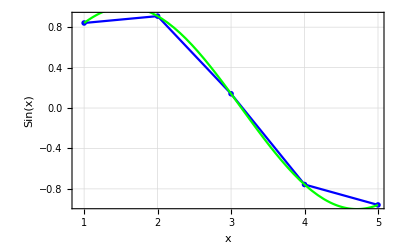

```mathematica
Show[
ListLinePlot[datos,
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["Sin(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}
],
Plot[Sin[x],{x,1,5},PlotStyle->Green]
]
```

## Ajuste

```mathematica
VandermondeMatrix[xList_]:=Quiet[Table[x^j /.Indeterminate->1,{x,xList},{j,0,Length[xList]-1}]];
PolynomialBase[n_]:=Table[x^j,{j,0,n-1}];
```

```mathematica
MatrixForm@VandermondeMatrix[datos[[All,1]]]
```

(1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16
1 | 3 | 9 | 27 | 81
1 | 4 | 16 | 64 | 256
1 | 5 | 25 | 125 | 625)

```mathematica
aVect= N@Inverse[VandermondeMatrix[datos[[All,1]]]].Transpose[{datos[[All,2]]}]
```

{{-0.649331},{2.36813},{-0.9503},{0.0680069},{0.00497029}}

```mathematica
MatrixForm[aVect]
```

(-0.649331
2.36813
-0.9503
0.0680069
0.00497029)

```mathematica
aList = First@Transpose[aVect]
```

{-0.649331,2.36813,-0.9503,0.0680069,0.00497029}

```mathematica
PolynomialBase[5]
```

{1,x,x^2,x^3,x^4}

```mathematica
aList.PolynomialBase[5]
```

-0.649331+2.36813 x-0.9503 x^2+0.0680069 x^3+0.00497029 x^4

Interpolación

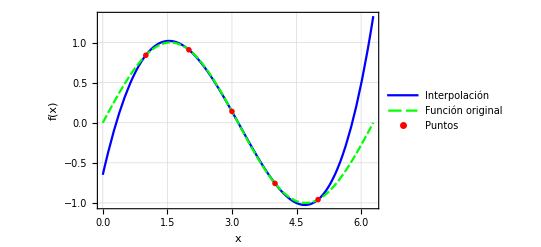

```mathematica
Show[
Plot[
{-0.6493310617421598+2.3681253386241767 x-0.9503004509420383 x^2+0.0680068658498752 x^3+0.00497029301803948 x^4,Sin[x]},
{x,0,2π},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Green},PlotLegends->{"Interpolación","Función original"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

Extrapolación

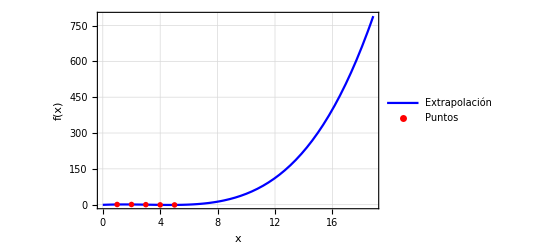

```mathematica
Show[
Plot[
-0.6493310617421598+2.3681253386241767 x-0.9503004509420383 x^2+0.0680068658498752 x^3+0.00497029301803948 x^4,
{x,0,6π},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},PlotLegends->{"Extrapolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

## Análisis del error

```mathematica
R[x_]:=Sin[x]-(-0.6493310617421598+2.3681253386241767 x-0.9503004509420383 x^2+0.0680068658498752 x^3+0.00497029301803948 x^4);
```

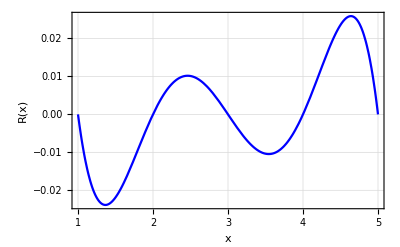

```mathematica
Plot[R[x],{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["R(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```

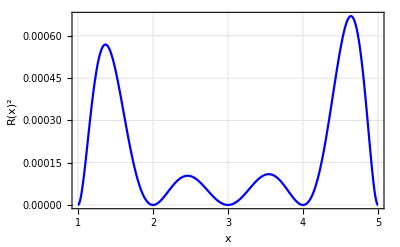

```mathematica
Plot[R[x]^2,{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["R(x)^2",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```

```mathematica
ϵ = √NIntegrate[R[x]^2,{x,a,b}]
```

0.0266467

## El problema de la interpolación polinomial

```mathematica
a = 1; b = 5;
GenerateData[Δ_]:=Table[{x,Sin[x]},{x,a,b,Δ}];
PolynomialInterpolation[data_]:=Block[{aVect,aList},
aVect= Quiet@N@Inverse[VandermondeMatrix[data[[All,1]]]].Transpose[{data[[All,2]]}];
aList = First@Transpose[aVect];

aList.PolynomialBase[Length[aList]]
];
```

```mathematica
datos = GenerateData[0.5]
```

{{1.,0.841471},{1.5,0.997495},{2.,0.909297},{2.5,0.598472},{3.,0.14112},{3.5,-0.350783},{4.,-0.756802},{4.5,-0.97753},{5.,-0.958924}}

```mathematica
PolynomialInterpolation[datos]
```

-0.0159075+1.06026 x-0.0965252 x^2-0.0809152 x^3-0.0463279 x^4+0.0238785 x^5-0.00309914 x^6+0.0000996397 x^7+3.21959×10^-6 x^8

```mathematica
errorVsData = Block[{data},Table[
data = GenerateData[Δ];
{Length[data],√NIntegrate[(Sin[x]-PolynomialInterpolation[data])^2,{x,a,b}]},
{Δ,0.05,0.5,0.05}
]
];
```

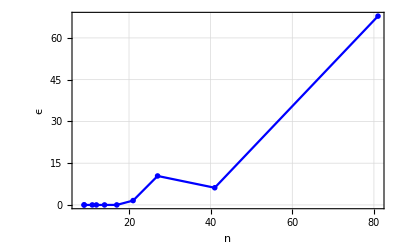

```mathematica
ListLinePlot[errorVsData,
PlotTheme->"Monochrome",FrameLabel->{Style["n",15], Style["ϵ",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```

```mathematica
muchosDatos = GenerateData[0.05]
```

{{1.,0.841471},{1.05,0.867423},{1.1,0.891207},{1.15,0.912764},{1.2,0.932039},{1.25,0.948985},{1.3,0.963558},{1.35,0.975723},{1.4,0.98545},{1.45,0.992713},{1.5,0.997495},{1.55,0.999784},{1.6,0.999574},{1.65,0.996865},{1.7,0.991665},{1.75,0.983986},{1.8,0.973848},{1.85,0.961275},{1.9,0.9463},{1.95,0.92896},{2.,0.909297},{2.05,0.887362},{2.1,0.863209},{2.15,0.836899},{2.2,0.808496},{2.25,0.778073},{2.3,0.745705},{2.35,0.711473},{2.4,0.675463},{2.45,0.637765},{2.5,0.598472},{2.55,0.557684},{2.6,0.515501},{2.65,0.472031},{2.7,0.42738},{2.75,0.381661},{2.8,0.334988},{2.85,0.287478},{2.9,0.239249},{2.95,0.190423},{3.,0.14112},{3.05,0.0914646},{3.1,0.0415807},{3.15,-0.00840725},{3.2,-0.0583741},{3.25,-0.108195},{3.3,-0.157746},{3.35,-0.206902},{3.4,-0.255541},{3.45,-0.303542},{3.5,-0.350783},{3.55,-0.397148},{3.6,-0.44252},{3.65,-0.486787},{3.7,-0.529836},{3.75,-0.571561},{3.8,-0.611858},{3.85,-0.650625},{3.9,-0.687766},{3.95,-0.723188},{4.,-0.756802},{4.05,-0.788525},{4.1,-0.818277},{4.15,-0.845984},{4.2,-0.871576},{4.25,-0.894989},{4.3,-0.916166},{4.35,-0.935053},{4.4,-0.951602},{4.45,-0.965773},{4.5,-0.97753},{4.55,-0.986844},{4.6,-0.993691},{4.65,-0.998054},{4.7,-0.999923},{4.75,-0.999293},{4.8,-0.996165},{4.85,-0.990547},{4.9,-0.982453},{4.95,-0.971903},{5.,-0.958924}}

```mathematica
interpolacionMuchosDatos = PolynomialInterpolation[GenerateData[0.1]]
```

-4.98708×10^-7+1.00001 x-0.0000119489 x^2-0.166652 x^3-0.0000184517 x^4+0.00833083 x^5-1.39163×10^-6 x^6-0.000216059 x^7-2.63838×10^-6 x^8+3.32888×10^-6 x^9+7.45364×10^-7 x^10-2.71045×10^-7 x^11+2.39478×10^-8 x^12-2.99823×10^-8 x^13-1.42063×10^-9 x^14+1.07817×10^-9 x^15-3.64183×10^-11 x^16-1.33037×10^-11 x^17-1.69817×10^-12 x^18-1.357×10^-13 x^19+3.07809×10^-14 x^20-2.21012×10^-14 x^21-5.49945×10^-15 x^22+2.52584×10^-15 x^23-1.07434×10^-15 x^24-5.57097×10^-17 x^25+3.62308×10^-17 x^26-3.60174×10^-19 x^27+1.03435×10^-18 x^28-9.77934×10^-21 x^29-1.20295×10^-20 x^30-4.37697×10^-21 x^31-3.69569×10^-21 x^32+2.38165×10^-22 x^33-2.01409×10^-23 x^34-3.0128×10^-23 x^35+3.16115×10^-25 x^36+2.82712×10^-26 x^37-4.34757×10^-26 x^38+5.66534×10^-27 x^39-1.27189×10^-28 x^40

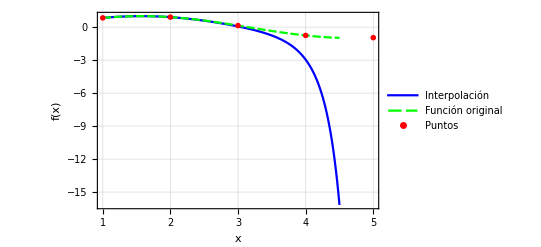

```mathematica
Show[
Plot[
{interpolacionMuchosDatos,Sin[x]},
{x,1,4.5},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Green},PlotLegends->{"Interpolación","Función original"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```